```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
tab = Import["./temp_chain_29-10-2026_123","Table"];
```

```mathematica
(*tab = Import["/home/kacpert/Documents/temp_26-10-2026/gausshamiltonian/examples/temp_1dchain_26-10-2026" , "Table"];*)
```

```mathematica
u = tab[[;; , 3]];
```

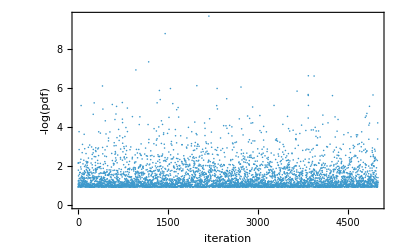

```mathematica
ListPlot[u , Axes->False , Frame->True , FrameLabel->{"iteration" , "-log(pdf)"} , PlotRange->All]
```

```mathematica
thr = 100;
```

```mathematica
chain = tab[[thr;; , 1]];
```

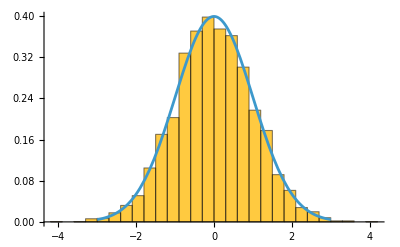

```mathematica
Show[Histogram[chain , {0.3} , "PDF"] , Plot[PDF[NormalDistribution[0 , 1.0] , x] , {x , -3 , 3}]]
```

```mathematica
(*-Log[PDF[NormalDistribution[0 , 1] , x]]//ComplexExpand//FullSimplify*)
```

```mathematica
(*%/.x->0.5*)
```

```mathematica
(*simple Metropolis Hastings:*)
```

```mathematica
(*link[x_]:= {x,1/2 (x^2+Log[2 π])};*)
```

```mathematica
(*iter[{x_ , u_}]:= Module[{ newx , newu , acc},
{newx , newu} = link[x + RandomReal[{-0.1 , 0.1}]];
acc = Min[1.0 , Exp[u - newu]];
If[RandomReal[] <= acc,
{newx , newu},
{x , u}
]
];*)
```

```mathematica
(*dtasimple = NestList[iter , link[0.0]  , 1000000];*)
```

```mathematica
(*Show[Histogram[dtasimple[[10000;; , 1]] , {0.2} , "PDF"] , Plot[PDF[NormalDistribution[0 , 1] , x] , {x , -3 , 3}]]*)
```